## Computing for Mathematical Physics 2022/23

# Homework 4

# Mark for homework 4: /42 (to be competed by your marker)

# Feedback from marker: (to be competed by your marker)

# Give your answers in the code cells marked (* Enter your solution here *)

Double click the vertical braces on the RHS of each of the question headings to open and view them.

1. Monte Carlo integration procedure to estimate π.  [20 marks]

a) Use Table and RandomReal to make a list of 100,000 points, called, shots, each one in the form of a two-element list {x,y}, with x values in the range -1 ≤ x ≤ 1 and y values in -2 ≤ y ≤ 2. You must use a semi-colon to terminate the Table command, to avoid filling the screen with 200,000 random numbers. Use ListPlot with option AspectRatio→Automatic, together with any other due formatting, to display the points.
[6 marks]

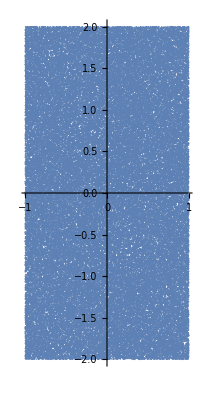

```mathematica
(* Enter code in a new cell immediately below this one. *)
Clear["Global`*"]
shots =Table[{RandomReal[{-1,1}], RandomReal[{-2,2}]},100000];
ListPlot[shots, AspectRatio->Automatic]
```

b) Write a function hitQ, using Which, that specifically takes a two element list, {x,y}, as input. If x^2+y^2≤1, the function should return True, and False otherwise.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
hitQ[{x_,y_}]:= If[x^2+y^2<=1, True, False]
```

c) Use Select with hitQ to generate a new list called hitList, comprised of those points inside shots with  x^2+y^2≤1. You must use a semi-colon to terminate the Table command, to avoid filling the screen with a few 10,000 random numbers. Use ListPlot with option AspectRatio→Automatic, together with any other due formatting, to view the hitList points.
[5 marks]

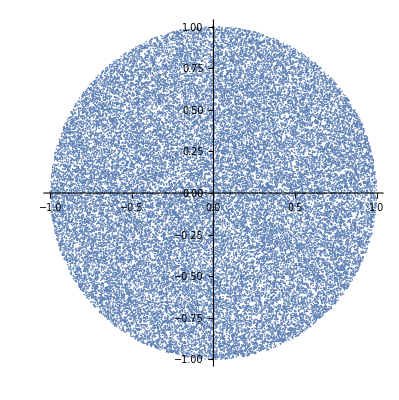

```mathematica
(* Enter code in a new cell immediately below this one. *)
hitList = Select[shots, hitQ] ;
ListPlot[hitList, AspectRatio->Automatic]
```

d) Compute the fraction of points inside shots with  x^2+y^2≤1, hitFraction.  
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
hitFraction = Length[hitList]/Length[shots]
```

39311/100000

e) By considering hitFraction together with the initial area covered with the points in shots, determine a numerical estimate for π. Display your estimate to 5 s.f. For full marks in this part, you will need to list your logic, clearly, in 2-3 short sentences, in a text cell.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

The radius of the circle is 1, so the area of the circle is π. The area of the rectangle in which all the points lie is 4×2=8, so the ratio of the area of the circle to the area of the rectangle is π/8. As the number of points tend to infinity the ratio of points in the circle divided by the total number of points, tends to π/8. Thus multiplying this ratio by 8 will give us an approximation of π.

```mathematica
pi = hitFraction*8
N[pi,5]
```

39311/12500

3.1449

2. Recursive function. [8 marks]

Let the function P_n(x) be defined by the recursion relation:
	
	n P_n(x)   =   (2n-1)  x  P_(n-1)(x)  -  (n-1) P_(n-2)(x) 

with P_0(x)=1, P_1(x) = x.

a) Implement the function P_n(x) as a recursive function called PA[n_,x_] using Which.

b) Implement the function P_n(x) again, now as PB[n_,x_], without using If or Which. Instead, carry out the implementation by providing three separate (overloaded) definitions for PB[n_,x_]:
i)   a definition specific to the n=0 case, PB[0,x_],
ii)  a definition specific to the n=1 case, PB[1,x_],
iii) a definition for all other general n values, PB[n_,x_].

c) Use Simplify together with the equal operator, ==, to test whether PA[15,x] and PB[15,x]equal Mathematica’s internal LegendreP[15,x] function. 
[8 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
```

```mathematica
Clear["Global`*"]
PA[n_,x_]:=Which[n==0, 1,n==1,x,True, ((2n-1)*x*PA[(n-1),x]-(n-1)*PA[(n-2),x])/n]
PB[n_,x_]:= ((2n-1)*x*PB[(n-1),x]-(n-1)*PB[(n-2),x])/n
PB[0,x_]=1
PB[1,x_]:=x
Simplify[PA[15,x]]== Simplify[LegendreP[15,x]]
Simplify[PB[15,x]]==Simplify[LegendreP[15,x]]
```

1

True

True

3. List manipulation with user defined functions.  [10 marks]

For this question you will need to evaluate the following code cell to store the list marks in memory, corresponding to fictitious student exam marks.

```mathematica
Clear["Global`*"]
marks={
{1,"Rishi","Sunak",13},
{2,"Donald","Trump",1},
{3,"Donald","Trump",0},
{3,"Rishi", "Sunak",17},
{1,"Liz","Truss",4},
{1,"Joe", "Biden",16},
{2,"Joe", "Biden",14},
{1,"Barak","Obama",22},
{1,"Theresa","May",17},
{2,"Liz","Truss",1},
{1,"Boris","Johnson"},
{2,"Theresa","May",11},
{2,"Boris","Johnson"},
{2,"Barak","Obama",25}
};
```

Each entry in the marks list has the form

	{test number, first name, family name, mark}

or, if a mark is missing,

	{test number, first name, family name} .

a) Write a function consolidate[data_], using Map and Rest, capable of taking in the list marks and removing the test number from the start of each entry. Apply your consolidate function to the list marks.
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
consolidate[data_]:= Map[Rest,data]
consolidate[marks]
```

{{Rishi,Sunak,13},{Donald,Trump,1},{Donald,Trump,0},{Rishi,Sunak,17},{Liz,Truss,4},{Joe,Biden,16},{Joe,Biden,14},{Barak,Obama,22},{Theresa,May,17},{Liz,Truss,1},{Boris,Johnson},{Theresa,May,11},{Boris,Johnson},{Barak,Obama,25}}

b) Extend your  consolidate[data_] function so as to additionally apply a replacement rule to its output before it is returned. The replacement rule should act to consolidate the marks for each student, so that each student entry in the final output list is of the form

	{first name, family name, test1_mark, test2_mark,...}

I.e., the final output list should have only one member per student.

Each member of the final output list should only contain test marks for tests attempted by the student named in that member, i.e., each member may have a different length.

Apply this modified consolidate function to the list marks, and store the output as consolidatedMarks.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
replacementrule = {a___, {b_,c_,d___},e___,{b_,c_,f___},g___}:> {a,{b,c,d,f},e,g}
consolidate[data_]:=Map[Rest,data]//.replacementrule
consolidatedMarks=consolidate[marks]
```

{a___,{b_,c_,d___},e___,{b_,c_,f___},g___}:>{a,{b,c,d,f},e,g}

{{Rishi,Sunak,13,17},{Donald,Trump,1,0},{Liz,Truss,4,1},{Joe,Biden,16,14},{Barak,Obama,22,25},{Theresa,May,17,11},{Boris,Johnson}}

c) Define a function orderedFirstNamesQ[member1_,member2_] designed to take two members from the consolidatedMarks list as input. This function should, itself, use OrderedQ to determine whether member1 and member2 are input in alphabetical order, according to the first name contained within each one. If member1 and member2 have been input to the function in alphabetical order, as determined by examining the first name in each input member, orderedFirstNamesQ should return True, otherwise return False.

Use Sort together with the orderedFirstNamesQ function to rearrange the members of consolidatedMarks such that their first names appear in  alphabetical order.
[4 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
orderedFirstNamesQ[member1_,member2_]:= If[OrderedQ[{member1[[1]],member2[[1]]}],True,False]
consolidatedMarks=Sort[consolidatedMarks]
```

{{Boris,Johnson},{Barak,Obama,22,25},{Donald,Trump,1,0},{Joe,Biden,16,14},{Liz,Truss,4,1},{Rishi,Sunak,13,17},{Theresa,May,17,11}}

Was not sure on how the question wanted me to approach the sorting of the list but the Sort function can already sort the members of the list based on their first names, given that the first name is the first element of each sublist.

4. Pure functions.  [4 marks]

In this question we seek to compute a very basic numerical approximation to the integral of the function x^2 Cos[x]^2 over the range 0<=x<=3.5π, based on approximating the area under the function in this range by a number of thin rectangles, each of the same width.

Set rectangleWidths=0.00001;

Set rectangleUpperEdges=Range[rectangleWidths,3.5π,rectangleWidths];

a) Create a list of values, called rectangleHeights, by passing rectangleUpperEdges to Map, together with a pure function representation of x^2 Cos[x]^2. [I.e. if the i’th element in rectangleUpperEdges has a value, say, x_i, then the i’th element of rectangleHeights should have a value x_i^2 Cos[x_i]^2.] 
[2 marks]

```mathematica
(* Enter code in a new cell immediately below this one. *)
Clear["Global`*"]
rectangleWidths=0.00001;
rectangleUpperEdges=Range[rectangleWidths,3.5π,rectangleWidths];
rectangleHeights = Map[Function[x,x^2 Cos[x]^2], rectangleUpperEdges];
```

b) Create a list called rectangleAreas, by passing rectangleHeights to Map, together with a suitably defined pure function, to multiply each element in rectangleHeights by the constant rectangleWidths.
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
rectangleAreas = Map[Function[x,rectangleWidths*x],rectangleHeights];
```

c) Compute the sum of the elements in rectangleAreas, and compare it to what one obtains when one integrates x^2 Cos[x]^2 over 0<=x<=3.5π using Mathematica’s native Integrate function.
[1 mark]

```mathematica
(* Enter code in a new cell immediately below this one. *)
Sum[rectangleAreas[[i]], {i,1,Length[rectangleAreas]}]
Integrate[x^2 Cos[x]^2,{x,0,3.5π}]
```

218.817

218.817

Total marks available: 42

Solutions are due by 1200 noon on Thursday February 9th here:  allow time for uploading on moodle.

A 10% mark deduction will be made (4 marks) if the template isn’t used.

Name your solution notebook file in the format WK4_HMWK_<Initials>_<Family Name>.nb, e.g. WK4_HMWK_K_Hamilton.nb

Make a backup copy of your solutions.

Delete all cell evaluation output by selecting Cell → Delete All Output from the drop-down menus at the top of the screen, then save and upload that file to Moodle.

The first thing your marker will do when they receive your notebook is to evaluate all of it, to regenerate the output, by clicking Evaluation → Evaluate Notebook from the drop-down menus at the top of the screen. It is your responsibility to check that carrying out this process will produce the output you intend it to, before you upload your work.

K. Hamilton, J. Bhamrah, J. Underwood, L. McKemmish — UCL
Last revision 09:16 30 Nov 2022